```mathematica
lst=Import["matcode/prj_min_len/doc/lmin_od.txt","list"]
```

{1.5246,1.7851,1.9708,2.1226,2.254,2.3715,2.4787,2.5779,2.6707,2.7581,2.841,2.92,2.9956,3.0683,3.1382,3.2058,3.2712,3.3347,3.3963,3.4563,3.5148,3.5718,3.6275,3.682,3.7353,3.7876,3.8388,3.889,3.9384,3.9869,4.0345,4.0814,4.1275,4.1729,4.2177,4.2618,4.3052,4.3481,4.3904,4.4322,4.4734,4.5141,4.5543,4.5941,4.6334,4.6722,4.7107,4.7487,4.7863,4.8235,4.8603,4.8968,4.933,4.9687,5.0042,5.0393,5.0741,5.1086,5.1428,5.1767,5.2103,5.2436,5.2767,5.3095,5.342,5.3743,5.4063,5.4381,5.4697,5.501,5.5321,5.563,5.5937,5.6241,5.6544,5.6844,5.7143,5.7439,5.7734,5.8027,5.8317,5.8606,5.8894,5.9179,5.9463,5.9745,6.0026,6.0304,6.0582,6.0857,6.1131,6.1404,6.1675,6.1945,6.2213,6.248,6.2745,6.3009,6.3272}

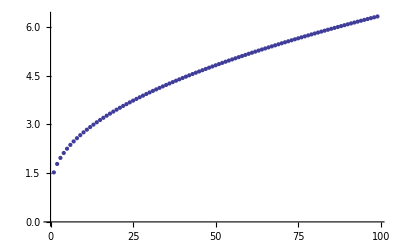

```mathematica
g1=ListPlot[lst]
```

```mathematica
fm[a_,b_,c_]:=Sum[(a+√(b+i)/c-lst[[i]])^2,{i,Length[lst]}]
FindMinimum[fm[a,b,c],{{a,1},{b,0.5},{c,2}}]
```

{0.000278697,{a→1.15323,b→-0.513038,c→1.91731}}

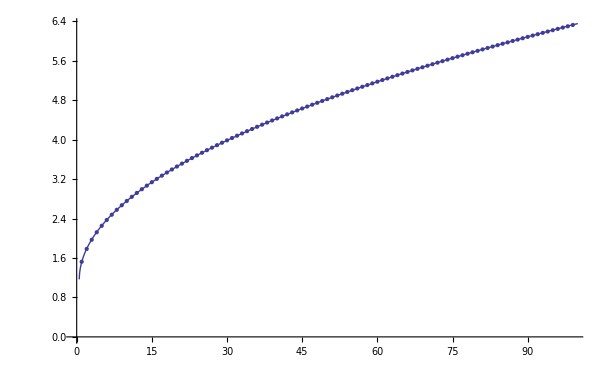

```mathematica
g2=Plot[1.153+√(-0.513+x)/1.917,{x,0,100}];
Show[g1,g2]
```

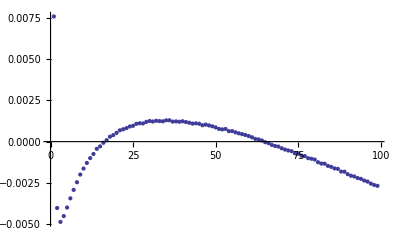

```mathematica
ListPlot[lst-Table[1.153+√(-0.513+i)/1.917,{i,1,Length[lst]}]]
```

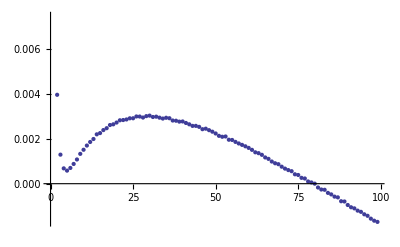

```mathematica
ListPlot[lst-Table[1.153+√(-0.550+i)/1.917,{i,1,Length[lst]}]]
```

```mathematica
fm2[a_,b_,c_]:=Sum[(a+√(b+i/c)-lst[[i]])^2,{i,Length[lst]}]
FindMinimum[fm2[a,b,c],{{a,1},{b,0.1},{c,4}}]
```

{0.000278697,{a→1.15323,b→-0.139562,c→3.67606}}

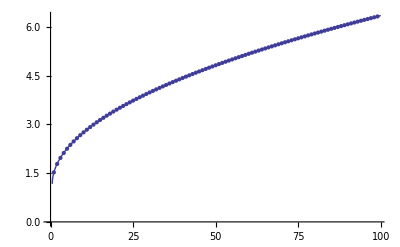

```mathematica
g2=Plot[1.153+√(-0.139+x/3.676),{x,0,100}];
Show[g1,g2]
```

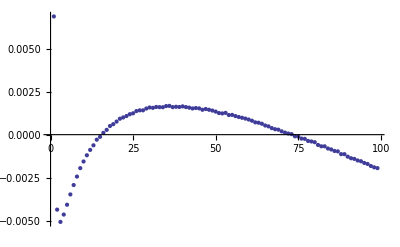

```mathematica
ListPlot[lst-Table[1.153+√(-0.139+i/3.676),{i,1,Length[lst]}]]
```

```mathematica
fm3[a_,b_,c_,d_]:=Sum[(a+(b+i)^d/c-lst[[i]])^2,{i,Length[lst]}]
sol3=FindMinimum[fm3[a,b,c,d],{{a,1},{b,-0.5},{c,2},{d,0.5}}]
```

{0.0000111934,{a→1.11053,b→-0.415777,c→1.85648,d→0.494553}}

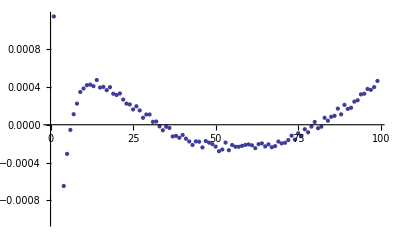

```mathematica
ListPlot[lst-Table[a+(b+i)^d/c/.sol3[[2]],{i,1,Length[lst]}]]
```

```mathematica
(* p-value=0.05 *)
```

```mathematica
lst=Import["matcode/prj_min_len/doc/lmin_od_pv=5e-2.txt","List"];
```

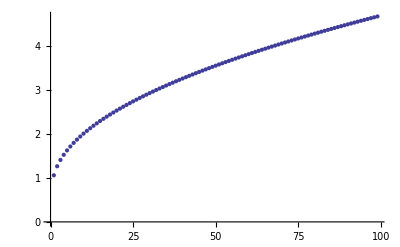

```mathematica
g1=ListPlot[lst]
```

```mathematica
fm[a_,b_,c_]:=Sum[(a+√(b+i)/c-lst[[i]])^2,{i,Length[lst]}]
sol=FindMinimum[fm[a,b,c],{{a,1},{b,0.5},{c,2}}]
```

{0.000530912,{a→0.821941,b→-0.653815,c→2.5729}}

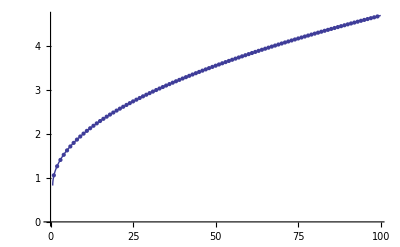

```mathematica
g2=Plot[0.821+√(-0.653+x)/2.572,{x,0,100}];
Show[g1,g2]
```

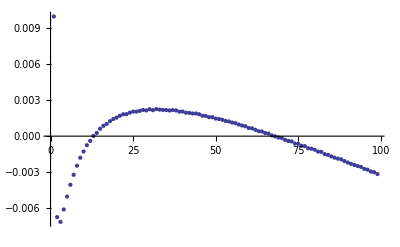

```mathematica
ListPlot[lst-Table[0.821+√(-0.653+i)/2.572,{i,1,Length[lst]}]]
```

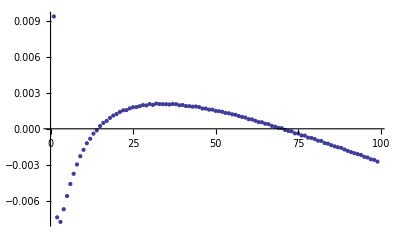

```mathematica
ListPlot[lst-Table[a+√(b+i)/c/.sol[[2]],{i,1,Length[lst]}]]
```

```mathematica
lst1=Import["matcode/prj_min_len/doc/lmin_od_pv=1e-2.txt","list"];
lst2=Import["matcode/prj_min_len/doc/lmin_od_pv=2e-2.txt","List"];
lst5=Import["matcode/prj_min_len/doc/lmin_od_pv=5e-2.txt","List"];
lst05=Import["matcode/prj_min_len/doc/lmin_od_pv=5e-3.txt","List"];
```

```mathematica
g1=ListPlot[lst1,PlotStyle->Hue[0.0]];
g2=ListPlot[lst2,PlotStyle->Hue[0.3]];
g5=ListPlot[lst5,PlotStyle->Hue[0.6]];
g05=ListPlot[lst05,PlotStyle->Hue[0.9]];
```

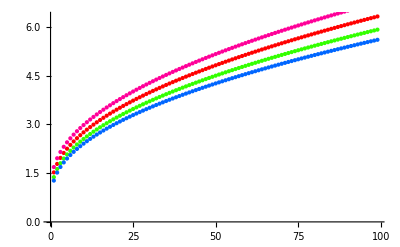

```mathematica
Show[g1,g2,g5,g05]
```

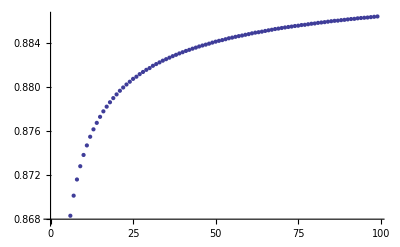

```mathematica
ListPlot[lst5/lst1]
```

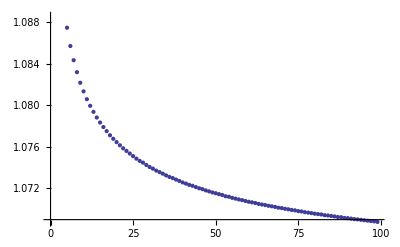

```mathematica
ListPlot[lst05/lst1]
```

0.0117753

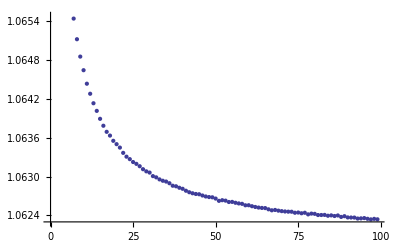

0.0350972

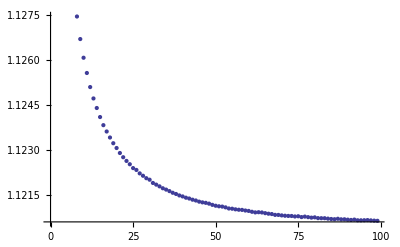

```mathematica
bs=-0.6;
(lst1[[1]]-bs)/(lst2[[1]]-bs)-(Last[lst1]-bs)/(Last[lst2]-bs)
ListPlot[(lst1-bs)/(lst2-bs)]
bs=-0.35;
(lst1[[1]]-bs)/(lst5[[1]]-bs)-(Last[lst1]-bs)/(Last[lst5]-bs)
ListPlot[(lst1-bs)/(lst5-bs)]
```

```mathematica
fm[a_,b_,c_,lst_]:=Sum[(a+√(b+i)/c-lst[[i]])^2,{i,Length[lst]}]
sol05=FindMinimum[fm[a,b,c,lst05],{{a,1},{b,-0.5},{c,2}}]
sol1=FindMinimum[fm[a,b,c,lst1],{{a,1},{b,-0.5},{c,2}}]
sol2=FindMinimum[fm[a,b,c,lst2],{{a,1},{b,-0.5},{c,2}}]
sol5=FindMinimum[fm[a,b,c,lst5],{{a,1},{b,-0.3},{c,2}}]
```

{0.000184532,{a→1.27627,b→-0.45891,c→1.80882}}

{0.000278697,{a→1.15323,b→-0.513038,c→1.91731}}

{0.000406399,{a→1.04648,b→-0.568829,c→2.03444}}

{0.000761964,{a→0.986308,b→-0.653719,c→2.14407}}

```mathematica
fm[a_,b_,c_,lst_]:=Sum[(a+c √(b+i)-lst[[i]])^2,{i,Length[lst]}]
sol5=FindMinimum[fm[a,b,c,lst5],{{a,1},{b,-0.3},{c,0.5}}]
sol2=FindMinimum[fm[a,b,c,lst2],{{a,1},{b,-0.5},{c,0.5}}]
sol1=FindMinimum[fm[a,b,c,lst1],{{a,1},{b,-0.5},{c,0.5}}]
sol05=FindMinimum[fm[a,b,c,lst05],{{a,1},{b,-0.5},{c,0.5}}]
```

{0.000761964,{a→0.986308,b→-0.653719,c→0.466404}}

{0.000406399,{a→1.04648,b→-0.568829,c→0.491536}}

{0.000278697,{a→1.15323,b→-0.513038,c→0.521565}}

{0.000184532,{a→1.27627,b→-0.45891,c→0.552847}}